## Building ANNs

### Multilayer perceptron on MNIST

```mathematica
mnistTrain=ResourceData["MNIST","TrainingData"];
mnistTest=ResourceData["MNIST","TestData"];
```

```mathematica
Clear[netModel];
netModel=NetChain[{
FlattenLayer[],
LinearLayer[16,"Input"->28*28],
LinearLayer[16,"Input"-> 16],
LinearLayer[10,"Input"->16],
SoftmaxLayer[]
},
"Input"->NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}],
"Output"->NetDecoder[{"Class",Range[0,9]}]
]
```

NetChain[…]

```mathematica
net=NetInitialize[netModel]
```

NetChain[…]

```mathematica
annSummaryGraphic=Information[net,"SummaryGraphic"]
```

-Graphics-

```mathematica
annSummaryGraphic=Show[annSummaryGraphic,ImageSize->{500,42}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/08-ann-summary-graphic.pdf",annSummaryGraphic]
```

/home/jam/Kuweta/mma_lessons/code/pics/08-ann-summary-graphic.pdf

```mathematica
trainedNet=NetTrain[net,mnistTrain,ValidationSet->mnistTest]
```

NetChain[…]

```mathematica
NetMeasurements[trainedNet,mnistTest,"Accuracy"]
```

0.9191

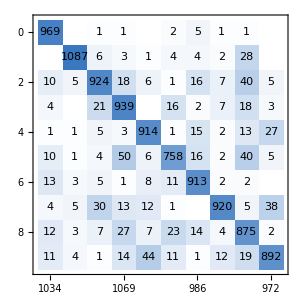
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[trainedNet,"MNIST","ConfusionMatrixPlot"]
```

```mathematica
Information[trainedNet]
```

Net Information

### Small test

```mathematica
(*Used  the  same  sample  as  in  08-using-anns.nb*)
img=Import[NotebookDirectory[]<>"data/4738-v3.png"];
img=ImageCrop[ImageRotate[img,Pi/2]];
```

```mathematica
y=50;ds=270; dw=11;
digits=Table[ImageResize[ImageTrim[img,{{x ds,y},{x ds+28dw,y+28 dw}}],{28,28}],{x,0,3,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
trainedNet[digits]
```

{1,2,3,3}